```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 387 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
(* Discussion of initial conditions, making initial velocities too big, and spring constant k too small , overshoots *) 
(* Discussion of x1 x2 and x2 being displacements from equilibrium *)
```

```mathematica
Clear[q]
q = { x1[t] , x2[t] , x3[t] }
```

{x1[t],x2[t],x3[t]}

```mathematica
D[q, t]
```

{x1'[t],x2'[t],x3'[t]}

```mathematica
D[q, t] . D[q, t]
```

x1'[t]^2+x2'[t]^2+x3'[t]^2

```mathematica
Clear[T]
T = 1/2 m ( D[q, t] . D[q, t] )
```

1/2 m (x1'[t]^2+x2'[t]^2+x3'[t]^2)

```mathematica
?Differences
```

```mathematica
Differences[ q ] 
Differences[ q ] [[1]]
Differences[ q ] [[2]]
```

{-x1[t]+x2[t],-x2[t]+x3[t]}

-x1[t]+x2[t]

-x2[t]+x3[t]

```mathematica
Sum[ ( Differences[ q ] [[i]] )^2 , { i, 1, 2 } ]
```

(-x1[t]+x2[t])^2+(-x2[t]+x3[t])^2

```mathematica
Clear[V]
V = 1/2 k Sum[ ( Differences[ q ] [[i]] )^2 , { i, 1, 2 } ] ;
V // TraditionalForm
```

1/2 k ((x2(t)-x1(t))^2+(x3(t)-x2(t))^2)

```mathematica
Clear[ℒ]
ℒ = T - V
```

-1/2 k ((-x1[t]+x2[t])^2+(-x2[t]+x3[t])^2)+1/2 m (x1'[t]^2+x2'[t]^2+x3'[t]^2)

```mathematica
D[ ℒ , D[q[[1]], t] ] - D[ ℒ , q[[1]] ] 
D[ ℒ , D[q[[2]], t] ] - D[ ℒ , q[[2]] ] // Expand 
D[ ℒ , D[q[[3]], t] ] - D[ ℒ , q[[3]] ]
```

-k (-x1[t]+x2[t])+m x1'[t]

-k x1[t]+2 k x2[t]-k x3[t]+m x2'[t]

k (-x2[t]+x3[t])+m x3'[t]

```mathematica
Table[
D[ ℒ , D[q[[i]], t] ] - D[ ℒ , q[[i]] ]== 0  ,
{ i, 1, 3 } ] // TableForm
```

-k (-x1[t]+x2[t])+m x1'[t]==0
1/2 k (2 (-x1[t]+x2[t])-2 (-x2[t]+x3[t]))+m x2'[t]==0
k (-x2[t]+x3[t])+m x3'[t]==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

-k x1[t]+k x2[t]-m x1''[t]==0
k x1[t]-2 k x2[t]+k x3[t]-m x2''[t]==0
k x2[t]-k x3[t]-m x3''[t]==0

```mathematica
Clear[parameters]
parameters = { 
k-> 200 , 
m -> 20 
} ;
parameters // TableForm
```

k→200
m→20

```mathematica
eqs /. parameters  // TableForm
```

-200 x1[t]+200 x2[t]-20 x1''[t]==0
200 x1[t]-400 x2[t]+200 x3[t]-20 x2''[t]==0
200 x2[t]-200 x3[t]-20 x3''[t]==0

```mathematica
Clear[ics]
ics = { 
x1[0] == 0.1 , 
x1'[0]== 0.1 , 
x2[0] == 0, 
x2'[0] == - 0.05, 
x3[0] == 0.1 , 
x3'[0] ==  0.04 
} ;
ics // TableForm
```

x1[0]==0.1
x1'[0]==0.1
x2[0]==0
x2'[0]==-0.05
x3[0]==0.1
x3'[0]==0.04

```mathematica
Clear[solution]
solution[t_] = 
First[NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 100 } ]]
```

{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t],x3[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t] ]  , { t, 0, 10 } , PlotLabels-> q  ]
```

-Graphics-

```mathematica
solution[t]
solution[t][[1]]
solution[t][[1,2]]
```

{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t],x3[t]→InterpolatingFunction[…][t]}

x1[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 1 , 100 , 0.5  } ]
```

```mathematica
(* REDO THIS *)
Clear[tMax]
tMax = 10 ;
nFrames=100;
frames=Table[Graphics[{Gray,Thick,Line[{q[[1]],0} ,{ q[[2]], 0 } ,{ q[[3]] , 0 }],Darker[Red],Disk[{ q[[1]], 0 } , 0.05],Darker[Blue],Disk[{ q[[2]], 0 } ,0.05],Disk[{ q[[3]] ,0} ,0.05 ]}/.solution[t],PlotRange->{{0 ,0.6},{-0.5,0.5}},Background->Lighter[Cyan]],{t,tMax/nFrames,tMax,tMax/nFrames}];
ListAnimate[frames]
```

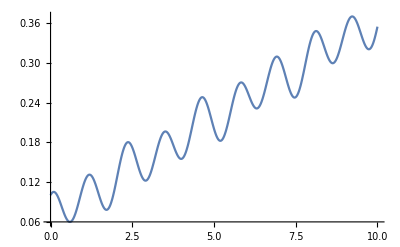

```mathematica
Plot[ q[[1]] /. solution[t] , { t, 0, 10 } ]
```

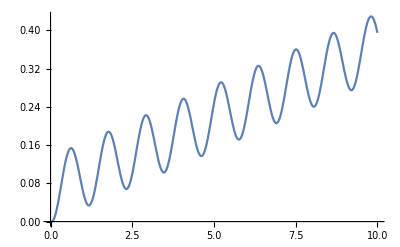

```mathematica
Plot[ q[[2]] /. solution[t] , { t, 0, 10 } ]
```

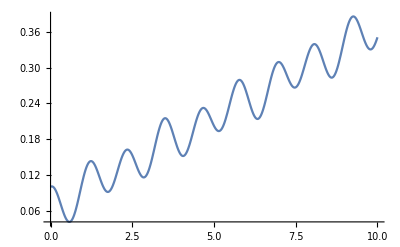

```mathematica
Plot[ q[[3]] /. solution[t] , { t, 0, 10 } ]
```